```mathematica
(* Task C-8 *)
Clear[p,q]
p[x_]=x^6-x^4-x^3-6 x^2+13 x-6;
q[x_]=x^3+4 x^2;
```

```mathematica
(* a *)
Factor[p[x]]
```

(-1+x)^3 (2+x) (3+x+x^2)

```mathematica
(* b *)
PolynomialQuotient[p[x],q[x],x]
```

-61+15 x-4 x^2+x^3

```mathematica
PolynomialRemainder[p[x],q[x],x]
```

-6+13 x+238 x^2

```mathematica
(* Second Method *)
PolynomialQuotientRemainder[p[x],q[x],x]
```

{-61+15 x-4 x^2+x^3,-6+13 x+238 x^2}

```mathematica
(* c *)
Integrate[p[x]/q[x],x]
```

3/(2 x)-61 x+(15 x^2)/2-(4 x^3)/3+x^4/4+(29 Log[x])/8+1875/8 Log[4+x]

```mathematica
NIntegrate[(p[x]-Log[x])/(√q[x]+Cos[x]^2),{x,1,ⅇ}]
```

16.0255

```mathematica
(* d *)
Clear[f,G]
f[x_,y_]:=q[y-x]*ArcTan[x+y];
G=ImplicitRegion[x^2+y^2≤4,{x,y}];
```

```mathematica
NIntegrate[f[x,y],{x,y}∈G,AccuracyGoal->10^-15]
```

-0.000601446

```mathematica
(* Task D-9 *)
Clear[w]
w[x_]:=x^3-3 x^2-3 ArcTan[x]+4;
```

```mathematica
(* a *)
FindRoot[w[x]==0,{x,1,3},WorkingPrecision->12]
```

{x→2.97032168797}

```mathematica
(* b *)
NMinimize[w[x],{x,1,3}]
```

{-3.34854,{x→2.08922}}

```mathematica
(* c *)
Clear[p]
p=Normal[Series[w[x],{x,2,4}]]
```

-3/5 (-2+x)+81/25 (-2+x)^2+114/125 (-2+x)^3+18/625 (-2+x)^4-3 ArcTan[2]

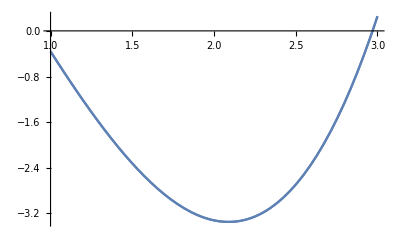

```mathematica
(* d *)
Show[{Plot[w[x],{x,1,3}],Plot[p,{x,1,3}]}]
```

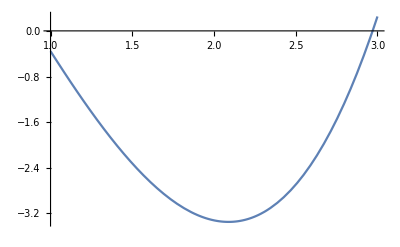

```mathematica
Plot[w[x],{x,1,3}]
```

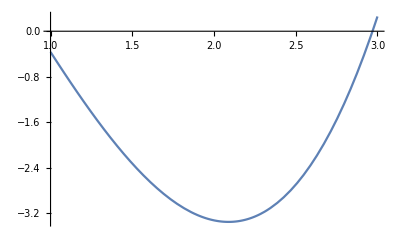

```mathematica
Plot[p,{x,1,3}]
```

```mathematica
(* e *)
M={2,w[2]};
Solve[w[2]==w'[2] 2+b,b]//N
```

{{b→-2.12145}}

```mathematica
w'[2]
```

-3/5

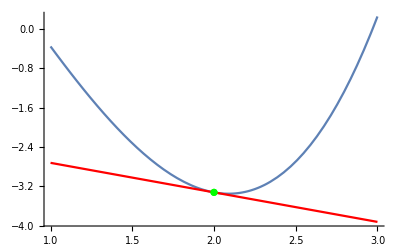

```mathematica
Show[{Plot[w[x],{x,1,3},PlotRange->All],Plot[-3/5 x-2.121446153382271,{x,1,3},PlotStyle->Red],ListPlot[{{M}},PlotStyle->Green]}]
```